IPPT Model

2c. Ambient Backfill Solver

	Instructions:
	- This notebook will evaluate the single-pulse model using a single set of initial conditions for constant neutral backfill 
	- This notebook is propellant agnostic
	
	How to Run:
	- Define the input conditions you desire under “Inputs”
	- Click “Evaluate Notebook” in Menu Options
	- Key performance metrics and steady-state and neutral diffusion will output for each pulse, use “3. Single Case Plots” to visualize model results

Inputs

```mathematica
(** From Single Case Solver **)
zmaxt=0.2;        (* Axial boundary of simulation *)
zstepst=500;       (* Number of axial gridpoints *)
tmaxt=8.88 10^-6;    (* Maximum time of simulation *)
tstepst=500;      (* Number of timesteps *)
zs0t=0.0;          (* Initial current sheet location *)
ws0t=0.005;       (* Initial current sheet width, or width of pre-ionized plasma *) 
χi0t=0.01;       (* Pre-ionization fraction *)
zχit=ws0t;        (* Pre-ionization length scale *)
nn0t=7.3 10^19;    (* Characteristic ambient neutral density *)
znt=0.01;     (* Characteristic ambient neutral length scale *)
Te0t=10;       (* Initial electron temperature *)
Ti0t=0.1;     (* Initial ion temperature *) 
Lct=2000 10^-9;   (* Coil inductance *)
L0t=600 10^-9;   (* Stray inductance *)
Rct=0.005;   (* Coil resistance *)
C0t=1 10^-6;   (* Capacitance *)
V0t=3000;    (* Capacitor voltage *)
zct=0.015;   (* Coil mutual coupling distance *)
zc0t = -0.002; (* Location of coil wrt neutral gas injection plane (Subscript[z, a]) *)
rtout= 0.075;   (* Thruster outer radius *)
rtin = 0.0225; (* Thruster inner radius *)

nn0zt[z_]=nn0t; (* Constant ambient backfill - do not adjust here *)

frept = 10000;
Npt = 1;
```

Solver and Data Visualization

t = 1.66080918 minutes

Isp = 12.2528 seconds

Thruster Efficiency w/o Energy Recovery = 0.00251745 %

Thruster Efficiency w/ Energy Recovery = 0.115187 %

Mass Utilization Efficiency = 2.20861 %

Plasma Density in the Current Sheet = 5.32015×10^18 m^-3

Mass Bit = 0.0156835 mg

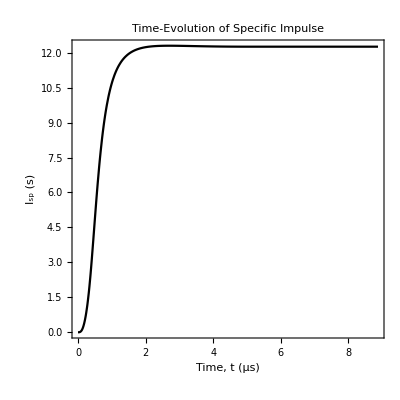

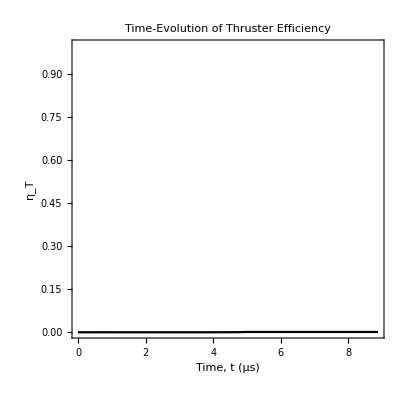

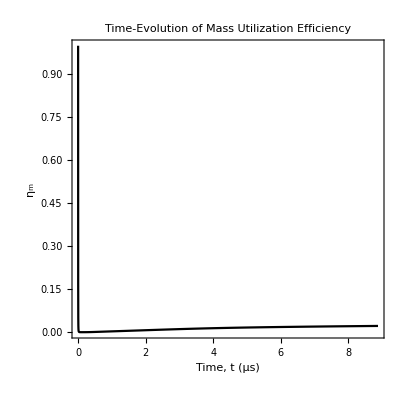

General::munfl: Exp[-670497.] is too small to represent as a normalized machine number; precision may be lost.

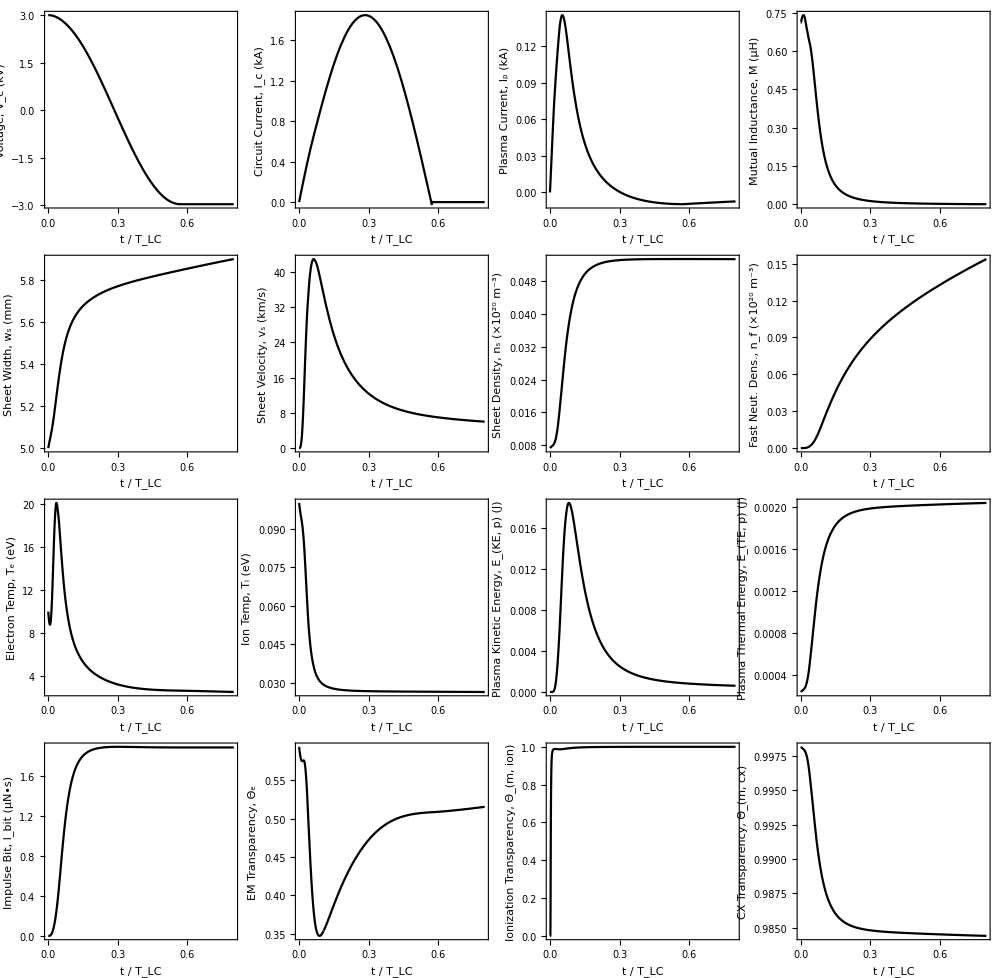

```mathematica
tval = AbsoluteTime[];
SPSolve[zmaxt,zstepst,tmaxt,tstepst,zs0t,ws0t,nn0t,χi0t,zχit,Te0t,Ti0t,znt,Lct,L0t,Rct,C0t,V0t,zct,zc0t,rtout,rtin,nn0zt];

(* Transparency Parameters *)
δs[t_]=δsd[L0t+Lct-Mout[t]^2/Lct,C0t,nsout[t],nnout[zsout[t],t]+nfout[t],Teout[t]];
Θs[t_]=Exp[-3wsout[t]/δs[t]];
Θmion[t_]=Exp[(-nsout[t]wsout[t]Sion[Teout[t]])/vsout[t]];
Θmcex[t_]=Exp[-nsout[t] wsout[t]σcx];

(** Print results **)
Print["t = ",(AbsoluteTime[]-tval)/60," minutes"];
Print["Isp = ",Isp[tmaxt]," seconds"];
Print["Thruster Efficiency w/o Energy Recovery = ", ηT[tmaxt]*100," %"];
Print["Thruster Efficiency w/ Energy Recovery = ",ηTrec[tmaxt]*100," %"];
Print["Mass Utilization Efficiency = ",ηm[tmaxt]*100," %"];
Print["Plasma Density in the Current Sheet = ", nsout[tmaxt]," m^-3"];
Print["Mass Bit = ",mbit*10^6," mg"];

(** Plot results **)
Print[TimePlot[Isp,"Specific Impulse","I_sp (s)",tmaxt]];
Print[EffTimePlot[ηTrec,"Thruster Efficiency","η_T",tmaxt]];
Print[EffTimePlot[ηm,"Mass Utilization Efficiency","η_m",tmaxt]];

Print[GraphicsGrid[{
{ScalePlot[Vout,"Voltage, V_c (kV)",10^-3],ScalePlot[Icout,"Circuit Current, I_c (kA)",10^-3],ScalePlot[Ipout,"Plasma Current, I_p (kA)",10^-3],ScalePlot[Mout,"Mutual Inductance, M (μH)",10^6]},
{ScalePlot[wsout,"Sheet Width, w_s (mm)",10^3],ScalePlot[vsout,"Sheet Velocity, v_s (km/s)",10^-3],ScalePlot[nsout,"Sheet Density, n_s (×10^20 m^-3)",10^-20],ScalePlot[nfout,"Fast Neut. Dens., n_f (×10^20 m^-3)",10^-20]},
{ScalePlot[Teout,"Electron Temp, T_e (eV)",1],ScalePlot[Tiout,"Ion Temp, T_i (eV)",1],ScalePlot[EkePl,"Plasma Kinetic Energy, E_(KE, p) (J)",1],ScalePlot[Ete,"Plasma Thermal Energy, E_(TE, p) (J)",1]},
{ScalePlot[Ibit,"Impulse Bit, I_bit (μN•s)",10^6],ScalePlot[Θs,"EM Transparency, Θ_e",1],ScalePlot[Θmion,"Ionization Transparency, Θ_(m, ion)",1],ScalePlot[Θmcex,"CX Transparency, Θ_(m, cx)",1]}
},Spacings-> {5,-5},ImageSize-> 1000]];
```

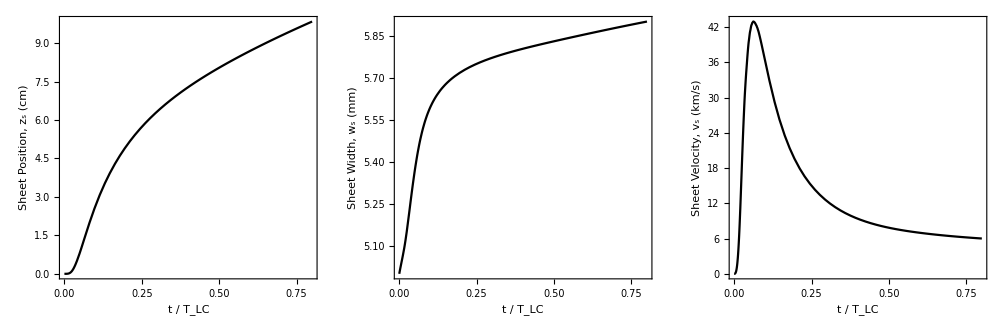

```mathematica
Print[GraphicsGrid[{
{ScalePlot[zsout,"Sheet Position, z_s (cm)",10^2],ScalePlot[wsout,"Sheet Width, w_s (mm)",10^3],ScalePlot[vsout,"Sheet Velocity, v_s (km/s)",10^-3]}
},Spacings-> {5,-5},ImageSize-> 1000]];
```